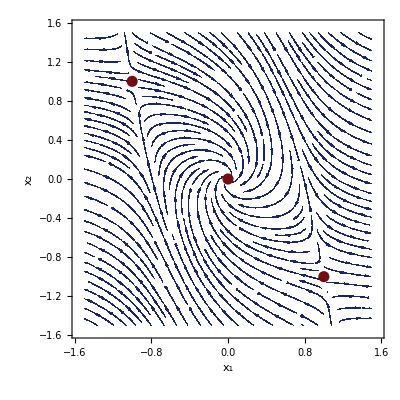

```mathematica
f1=-x1+2*x1^3+x2;
f2=-x1-x2;

p1 = StreamPlot[{f1,f2},{x1,-1.5,1.5},{x2,-1.5,1.5},
StreamPoints->Fine,Background->White,
FrameLabel->{TraditionalForm[Subscript[x,1]],TraditionalForm[Subscript[x,2]]},
Epilog->{
RGBColor[0.45,0.05,0.08],PointSize[0.02],
Point[{0,0}],Point[{1,-1}],Point[{-1,1}]
} ,
LabelStyle->{
FontFamily->"Latin Modern Math",
FontSize->14,
Black
},
StreamStyle->RGBColor[0.1,0.15,0.4],

StreamMarkers->"PinDart"
]

SetDirectory["/home/eva/Documents/ITMO/4_course/nonlinear/lab1/code/task1"];
Export["../../report/images/p1.pdf",p1,ImageResolution->600];
```

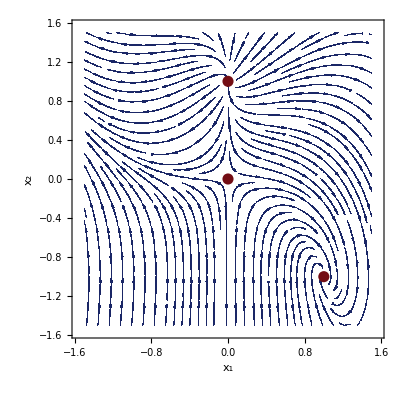

```mathematica
f1=x1+x1*x2;
f2=-x2+x2^2+x1*x2-x1^3;

p2 = StreamPlot[{f1,f2},{x1,-1.5,1.5},{x2,-1.5,1.5},
StreamPoints->Fine,Background->White,
FrameLabel->{TraditionalForm[Subscript[x,1]],TraditionalForm[Subscript[x,2]]},
Epilog->{
RGBColor[0.45,0.05,0.08],PointSize[0.02],
Point[{0,0}],Point[{0,1}],Point[{1,-1}]
} ,
LabelStyle->{
FontFamily->"Latin Modern Math",
FontSize->14,
Black
},
StreamStyle->RGBColor[0.1,0.15,0.4],

StreamMarkers->"PinDart"
]

Export["../../report/images/p2.pdf",p2,ImageResolution->600];
```

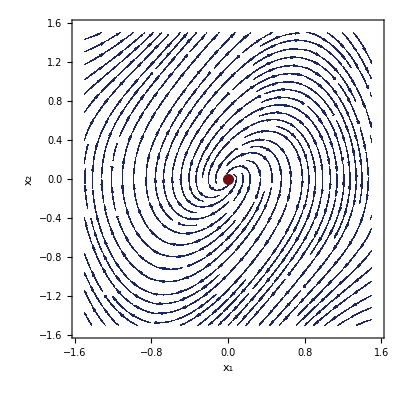

```mathematica
f1=x2;
f2=-x1 +x2*(1-x1^2+0.1*x1^4);

p3 = StreamPlot[{f1,f2},{x1,-1.5,1.5},{x2,-1.5,1.5},
StreamPoints->Fine,Background->White,
FrameLabel->{TraditionalForm[Subscript[x,1]],TraditionalForm[Subscript[x,2]]},
Epilog->{
RGBColor[0.45,0.05,0.08],PointSize[0.02],
Point[{0,0}]
} ,
LabelStyle->{
FontFamily->"Latin Modern Math",
FontSize->14,
Black
},
StreamStyle->RGBColor[0.1,0.15,0.4],

StreamMarkers->"PinDart"
]

Export["../../report/images/p3.pdf",p3,ImageResolution->600];
```

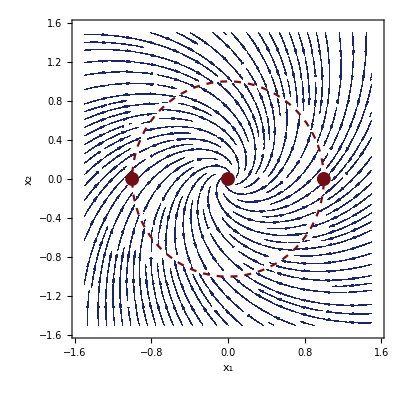

```mathematica
f1=(x1-x2)*(1-x1^2-x2^2);
f2=(x1+x2)*(1-x1^2-x2^2);

p4 = StreamPlot[{f1,f2},{x1,-1.5,1.5},{x2,-1.5,1.5},
StreamPoints->Fine,Background->White,
FrameLabel->{TraditionalForm[Subscript[x,1]],TraditionalForm[Subscript[x,2]]},
Epilog->{
RGBColor[0.45,0.05,0.08],Dashed,Thickness[0.004],Circle[{0,0},1],

PointSize[0.025],
Point[{0,0}],
Point[{-1,0}],
Point[{1,0}]
},
LabelStyle->{
FontFamily->"Latin Modern Math",
FontSize->14,
Black
},
StreamStyle->RGBColor[0.1,0.15,0.4],

StreamMarkers->"PinDart"
]

Export["../../report/images/p4.pdf",p4,ImageResolution->600];
```

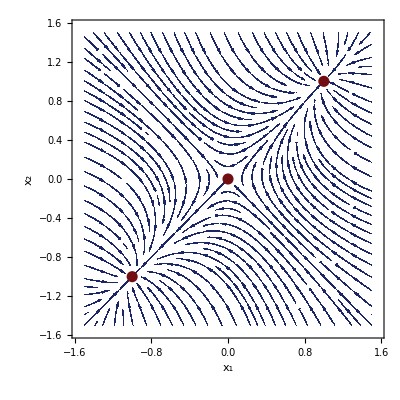

```mathematica
f1=-x1^3+x2;
f2=x1-x2^3;

p5 = StreamPlot[{f1,f2},{x1,-1.5,1.5},{x2,-1.5,1.5},
StreamPoints->Fine,Background->White,
FrameLabel->{TraditionalForm[Subscript[x,1]],TraditionalForm[Subscript[x,2]]},
Epilog->{
RGBColor[0.45,0.05,0.08],PointSize[0.02],
Point[{0,0}],Point[{-1,-1}],Point[{1,1}]
} ,
LabelStyle->{
FontFamily->"Latin Modern Math",
FontSize->14,
Black
},
StreamStyle->RGBColor[0.1,0.15,0.4],

StreamMarkers->"PinDart"
]

Export["../../report/images/p5.pdf",p5,ImageResolution->600];;
```

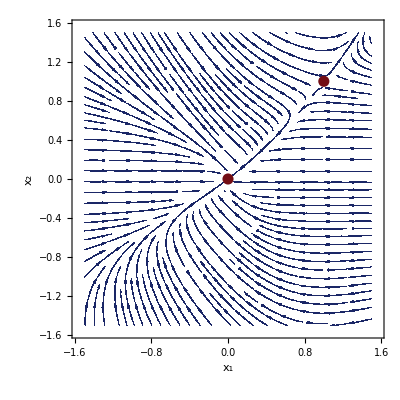

```mathematica
f1=-x1^3+x2^3;
f2=x2^3*x1-x2^3;

p6 = StreamPlot[{f1,f2},{x1,-1.5,1.5},{x2,-1.5,1.5},
StreamPoints->Fine,Background->White,
FrameLabel->{TraditionalForm[Subscript[x,1]],TraditionalForm[Subscript[x,2]]},
Epilog->{
RGBColor[0.45,0.05,0.08],PointSize[0.02],
Point[{0,0}],Point[{1,1}]
},
LabelStyle->{
FontFamily->"Latin Modern Math",
FontSize->14,
Black
},
StreamStyle->RGBColor[0.1,0.15,0.4],

StreamMarkers->"PinDart"
]

Export["../../report/images/p6.pdf",p6,ImageResolution->600];
```